#### Problem 9.3.23

Professor French’s Suggested method for part A

```mathematica
sol1=NDSolve[{x1'[t]==y1[t],y1'[t]==-4*Sin[x1[t]], x1[0]==.25,y1[0]==0},{x1,y1},{t,0,10}]
```

{{x1→InterpolatingFunction[{{0., 10.}}, <>],y1→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f1[t_]:=x1[t]/.sol1
```

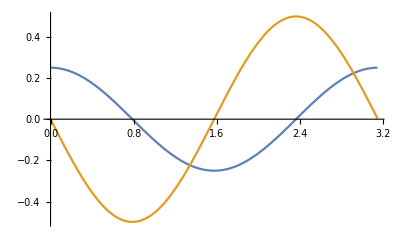

```mathematica
Plot[{f1[t],f1'[t]},{t,0,3.15}]
```

```mathematica
2
```

Part B

```mathematica
A=0.5
```

0.5

```mathematica
sol2=NDSolve[{x2'[t]==y2[t],y2'[t]==-4*Sin[x2[t]], x2[0]==.5,y2[0]==0},{x2,y2},{t,0,10}]
```

{{x2→InterpolatingFunction[{{0., 10.}}, <>],y2→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f2[t_]:=x2[t]/.sol2
```

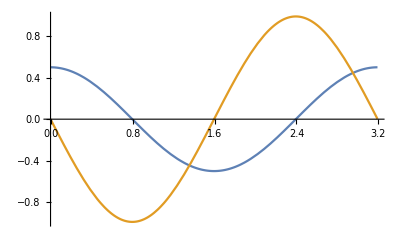

```mathematica
Plot[{f2[t],f2'[t]},{t,0,3.19}]
```

```mathematica
A=1.0
```

1.

```mathematica
sol3=NDSolve[{x3'[t]==y3[t],y3'[t]==-4*Sin[x3[t]], x3[0]==1.0,y3[0]==0},{x3,y3},{t,0,10}]
```

{{x3→InterpolatingFunction[{{0., 10.}}, <>],y3→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f3[t_]:=x3[t]/.sol3
```

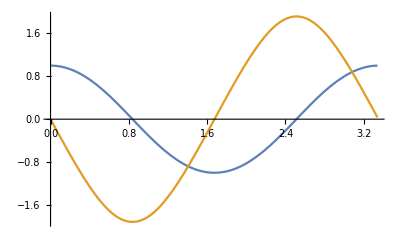

```mathematica
Plot[{f3[t],f3'[t]},{t,0,3.34}]
```

```mathematica
A=1.5
```

1.5

```mathematica
sol4=NDSolve[{x4'[t]==y4[t],y4'[t]==-4*Sin[x4[t]], x4[0]==1.5,y4[0]==0},{x4,y4},{t,0,10}]
```

{{x4→InterpolatingFunction[{{0., 10.}}, <>],y4→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f4[t_]:=x4[t]/.sol4
```

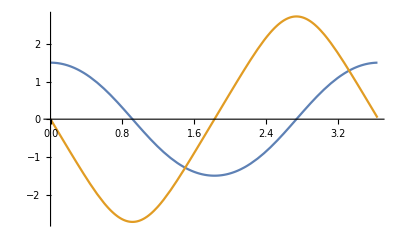

```mathematica
Plot[{f4[t],f4'[t]},{t,0,3.64}]
```

```mathematica
A=2.0
```

2.

```mathematica
sol5=NDSolve[{x5'[t]==y5[t],y5'[t]==-4*Sin[x5[t]], x5[0]==2.0,y5[0]==0},{x5,y5},{t,0,10}]
```

{{x5→InterpolatingFunction[{{0., 10.}}, <>],y5→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f5[t_]:=x5[t]/.sol5
```

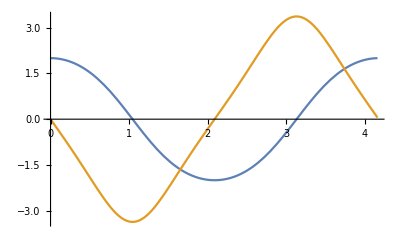

```mathematica
Plot[{f5[t],f5'[t]},{t,0,4.16}]
```

Part D

```mathematica
sol6=NDSolve[{x6'[t]==y6[t],y6'[t]==-4*Sin[x6[t]], x6[0]==4,y6[0]==0},{x6,y6},{t,0,10}]
```

{{x6→InterpolatingFunction[{{0., 10.}}, <>],y6→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f6[t_]:=x6[t]/.sol6
```

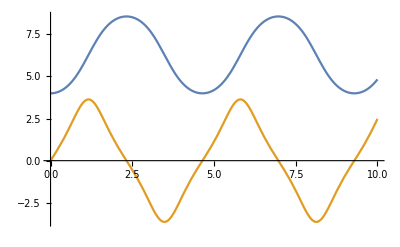

```mathematica
Plot[{f6[t],f6'[t]},{t,0,10}]
```

#### Problem 9.3.24

Part A

```mathematica
sol7=NDSolve[{x7'[t]==y7[t],y7'[t]==-4*Sin[x7[t]], x7[0]==0,y7[0]==2},{x7,y7},{t,0,10}]
```

{{x7→InterpolatingFunction[{{0., 10.}}, <>],y7→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f7[t_]:=x7[t]/.sol7
```

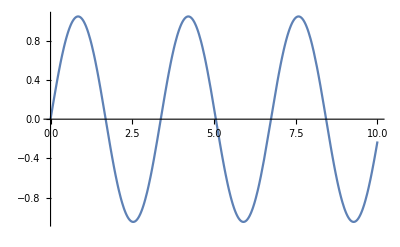

```mathematica
Plot[f7[t],{t,0,10}]
```

```mathematica
sol8=NDSolve[{x8'[t]==y8[t],y8'[t]==-4*Sin[x8[t]], x8[0]==0,y8[0]==5},{x8,y8},{t,0,10}]
```

{{x8→InterpolatingFunction[{{0., 10.}}, <>],y8→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
f8[t_]:=x8[t]/.sol8
```

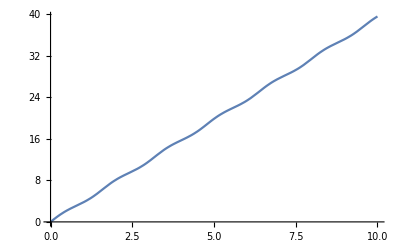

```mathematica
Plot[f8[t],{t,0,10}]
```

#### Problem 9.4.4

Part A

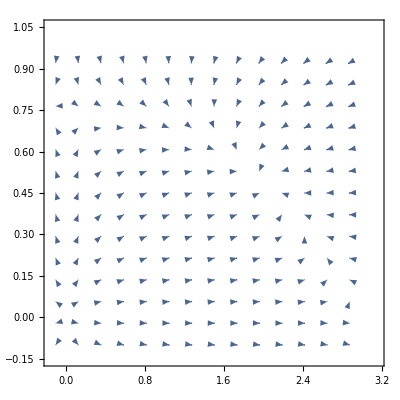

```mathematica
VectorPlot[{x*(1.5-0.5*x-y),y*(0.75-y-0.125x)},{x,-.1,3.1},{y,-.1,1},VectorScale->{.01,5}]
```

Part B

```mathematica
Solve[{x*(1.5-0.5*x-y)==0,y*(0.75-y-0.125x)==0},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.,y→0.75},{x→2.,y→0.5},{x→3.,y→0.},{x→0.,y→0.}}

Part C

```mathematica
j[x_,y_]:={{1.5-x-y,-x},{-0.125y,0.75-2y-0.125x}}
```

```mathematica
l[x_,y_]:=Det[j[x,y]-a*{{1,0},{0,1}}]
```

```mathematica
List[{j[0,0.75],j[2,0.5],j[3,0],j[0,0]}]
```

{{{{0.75,0},{-0.09375,-0.75}},{{-1.,-2},{-0.0625,-0.5}},{{-1.5,-3},{0.,0.375}},{{1.5,0},{0.,0.75}}}}

```mathematica
List[{Eigenvalues[j[0,0.75]],Eigenvalues[j[2,0.5]],Eigenvalues[j[3,0]],Eigenvalues[j[0,0]]}]
```

{{{-0.75,0.75},{-1.18301,-0.316987},{-1.5,0.375},{1.5,0.75}}}

```mathematica
N[List[{Eigenvectors[j[0,0.75]],Eigenvectors[j[2,0.5]],Eigenvectors[j[3,0]],Eigenvectors[j[0,0]]}]]
```

{{{{0.,1.},{0.998053,-0.0623783}},{{-0.995839,-0.0911256},{0.946337,-0.32318}},{{1.,0.},{-0.847998,0.529999}},{{-1.,0.},{0.,-1.}}}}

Part D

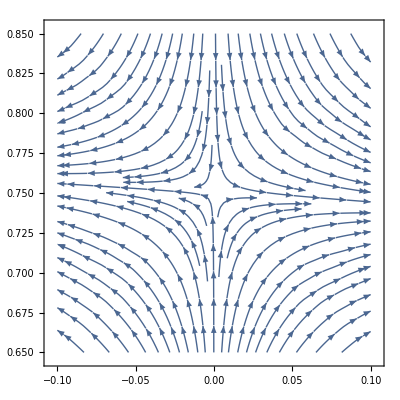

```mathematica
StreamPlot[{x*(1.5-0.5*x-y),y*(0.75-y-0.125x)},{x,-.1,.1},{y,.65,.85}]
```

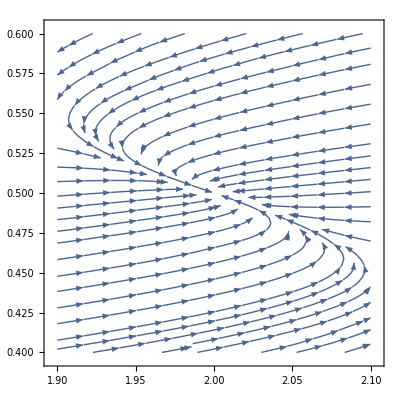

```mathematica
StreamPlot[{x*(1.5-0.5*x-y),y*(0.75-y-0.125x)},{x,1.9,2.1},{y,.4,.6}]
```

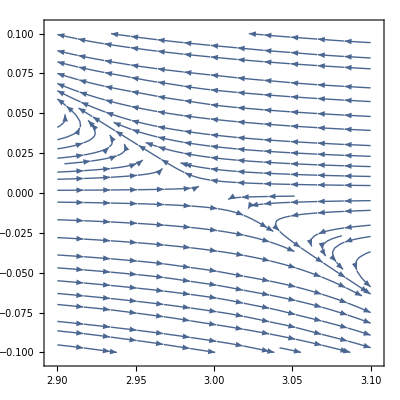

```mathematica
StreamPlot[{x*(1.5-0.5*x-y),y*(0.75-y-0.125x)},{x,2.9,3.1},{y,-.1,.1}]
```

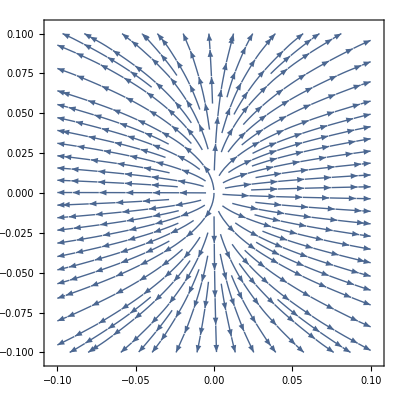

```mathematica
StreamPlot[{x*(1.5-0.5*x-y),y*(0.75-y-0.125x)},{x,-.1,.1},{y,-.1,.1}]
```

#### Problem 9.5.1

Part A

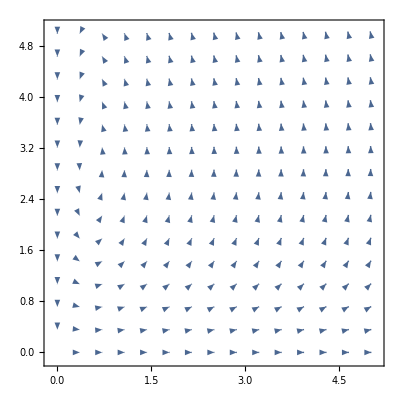

```mathematica
VectorPlot[{x*(1.5-0.5*y),y*(-0.5+x)},{x,0,5},{y,0,5},VectorScale->{.01,5}]
```

```mathematica
Eigenvalues[{{0,-.25},{3,0}}]
```

{0.+0.866025 ⅈ,0.-0.866025 ⅈ}

Part D,E

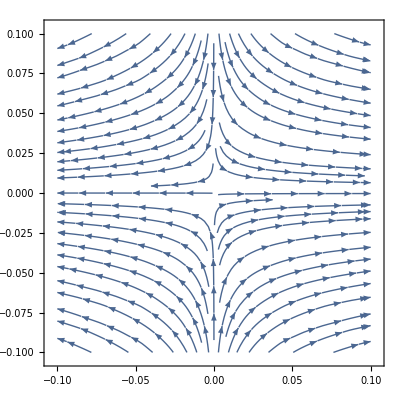

```mathematica
StreamPlot[{x*(1.5-0.5*y),y*(-0.5+x)},{x,-.1,.1},{y,-.1,.1}]
```

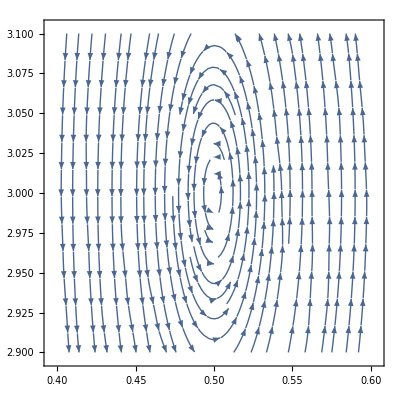

```mathematica
StreamPlot[{x*(1.5-0.5*y),y*(-0.5+x)},{x,0.4,.6},{y,2.9,3.1}]
```